```mathematica
link=Install[LinkConnect["44579@192.168.150.128,45163@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.45],ωbhe=7.5*Sqrt[0.45],ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
sol=With[{k=0.30,wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.23,0.0003] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

DispersionKit::warn: wstpDFindRoot - root finder failed at k1 = 0.11766 and k2 = 1.34486.

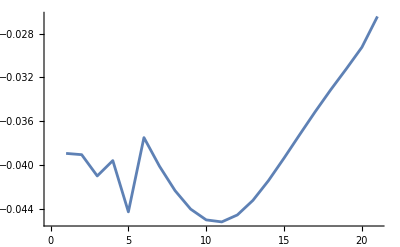

```mathematica
sol=With[{k=Range[0.3,1.5,0.05],wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[1.0575,-0.039] (1+0.0001 I {0,1,2}),MaxIterations->100]];


ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[17]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["2.txt",gama];
```

```mathematica
check=With[{k=Range[1.5,0.3,-0.05],wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[1.14,-0.08] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

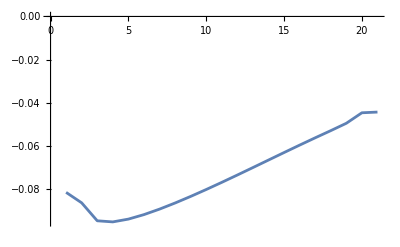

```mathematica
ListLinePlot[Im[check[[2,2]]]]
```